```mathematica
Exit[]
```

```mathematica
Needs["PM`"]

UninstallPackages[$PM,{"KnotToolsLink"}];
ClearAllCache[$PM];
LoadPackages[{"Geometries","KnotToolsLink"}]
```

Deleting package KnotToolsLink.

Deleting installation path.

Deleting files {/Users/jasoncantarella/Dropbox/Jason/PackageSources_2024-10-02T15:25:55/PackageSources/KnotToolsLink/PlanarDiagramObject_Library.nb}

WARNING: LTemplate has not yet been tested with Mathematica 14.1.0.
The latest supported Mathematica version is 12.3.1.
Please report any issues you find to szhorvat at gmail.com.

Updating package KnotToolsLink...

/Users/jasoncantarella/Dropbox/Jason/PackageSources_2024-10-02T15:25:55/PackageSources/KnotToolsLink/LibrarySources/PlanarDiagramObject/

Exporting library PlanarDiagramObject to /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/Source.

Names of functions in library PlanarDiagramObject are made public.

Current directory is: /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/Source

Unloading library PlanarDiagramObject ...

Generating library code ...

Compiling library code ...

Compilation done. Time elapsed = 19.2043

```mathematica
PD = Make["PlanarDiagramObject"]
```

PlanarDiagramObject[…]

```mathematica
InitFromPDCode[PD,Import["/Users/jasoncantarella/KnotTools/data/diagrams/hardunknots/OchaiIV.tsv"],0]
```

```mathematica
CompressDiagramInPlace[PD]
```

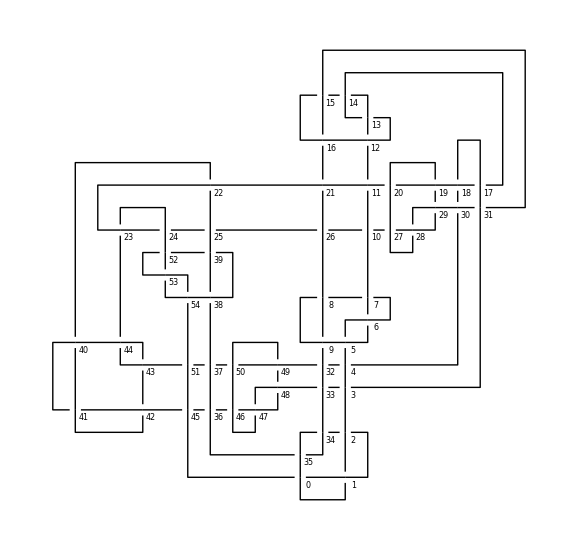

```mathematica
PlotDiagram[PD]
```

```mathematica
BuildConstraintMatrix[PD_] := 
SparseArray[Flatten[MapIndexed[{{#2[[1]],#1[[3]]+1}->-1,{#2[[1]],If[Abs[#1[[2]]-#1[[4]]]==1,Max[#[[{2,4}]]],0]+1}->+1}& ,PD],1],{Length[PD],2Length[PD]}];
```

```mathematica
BuildObjectiveFunction[PD_] :=(#.#)&@KirchhoffMatrix[CycleGraph[2*Length[PD]]]
```

```mathematica
BuildObjectiveFunction[PDCode[PD]]
```

SparseArray[…]

```mathematica
Timing[SuggestedLevels = QuadraticOptimization[BuildObjectiveFunction[PDCode@PD],{BuildConstraintMatrix[PDCode@PD],ConstantArray[-2,Length[PDCode@PD]]}];]
```

{0.006596,Null}

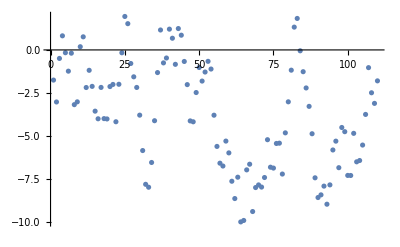

```mathematica
ListPlot[SuggestedLevels]
```

Here’s an experiment: what if we standardized the data by sort order to avoid different points being too close to each other.

```mathematica
DiscreteLevels = Flatten[Values@ KeySort@PositionIndex[Sort[MapIndexed[{#1,#2[[1]]}&,SuggestedLevels]][[All,2]]],1];
```

Now we need to construct new geometry according to the Levels embedding. We’ll need the ArcLines associated to the diagram. The strategy is to add a vertical segment to the curve at the first corner (or failing that, in the middle of the arc) which connects the levels at the start and end of the arc. So ArcLine[i] should be the line corresponding to arc[i] in the PD code.

The value SuggestedLevels[[i]] is the height at the crossing at start of the (outgoing) arc i-1.

```mathematica
LevelsEmbedding[PD_,L_]:= Block[{augmentedArcLines,al,procL,Lm=2,almost},
al = ArcLines[Spherogram[PD]];
procL = Association[
Join[Table[i->Floor[Lm*L[[i+1]]],{i,0,Length[L]-1}],{-1->Floor[Lm*Last[L]]}]];
augmentedArcLines =Table[ 
If[Length[#]==2,
{#[[1]],Mean[#],Mean[#],#[[2]]},
Join[#[[1;;2]],#[[2;;]]]
]& @ al[i],
{i,0,Length[Keys[al]]-1}];
almost = Flatten[Table[
Join[
Append[procL[i-2]]/@augmentedArcLines[[i,1;;2]],
Append[procL[i-1]]/@augmentedArcLines[[i,2;;]]
],{i,1,Length[al]} 
],1];
If[Norm[First[almost]-Last[almost]]>10.0^(-8),Append[almost,First[almost]],almost]
]
```

```mathematica
Graphics3D[Tube[LevelsEmbedding[PD,DiscreteLevels],1.0],ViewPoint->Top,ViewProjection->"Orthographic",ViewVertical->{0, 0, 1}]
```

-Graphics3D-

Now we need to rotate this to get some new perspectives on everything. If we just choose left or right we’ll have a lot of

```mathematica
R = RandomVariate[CircularRealMatrixDistribution[3]]
```

{{-0.144208,-0.510457,0.847725},{-0.792929,-0.452905,-0.407604},{-0.592004,0.730965,0.339444}}

```mathematica
Graphics3D[Tube[LevelsEmbedding[PD,DiscreteLevels].R,1],ViewPoint->Above]
```

-Graphics3D-

```mathematica
NewPD = Make["PlanarDiagramObject"]
```

PlanarDiagramObject[…]

```mathematica
InitFromCoordinates[NewPD,LevelsEmbedding[PD,DiscreteLevels].R]
```

```mathematica
CompressDiagramInPlace[NewPD]
```

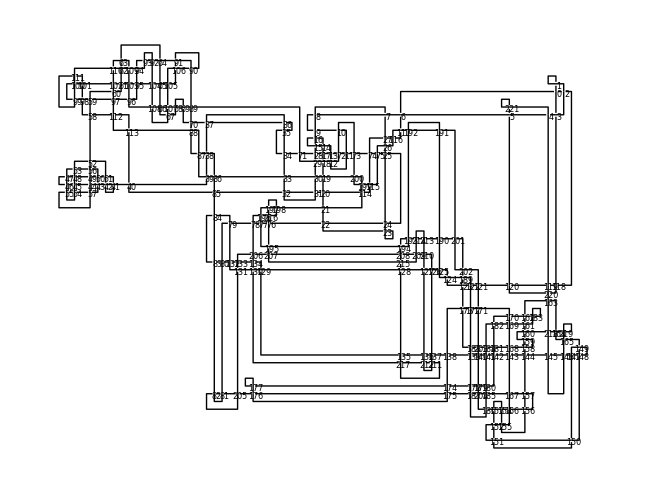

```mathematica
PlotDiagram[NewPD]
```

```mathematica
SimplifyDiagram4[NewPD]
```

<|Reidemeister I moves→0,Reidemeister Ia moves→0,Reidemeister II moves→0,Reidemeister IIa moves→0,Twist moves→0,Four moves→0,Diagram→PlanarDiagramObject[…]|>

```mathematica
NewPDSimplified = SimplifyDiagram[NewPD]["Diagram"]
```

PlanarDiagramObject[…]

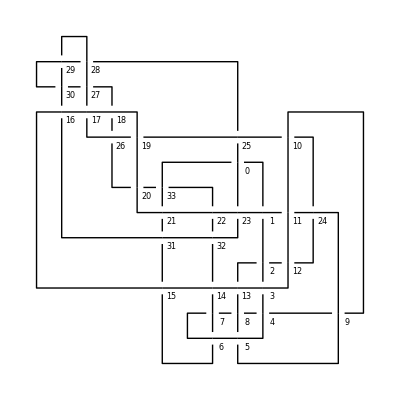

```mathematica
PlotDiagram[NewPDSimplified]
```

```mathematica
PDCode[NewPDSimplified]
```

{{67,48,0,49,-1},{0,25,1,26,-1},{32,2,33,1,1},{2,14,3,13,1},{8,4,9,3,1},{29,4,30,5,-1},{62,6,63,5,1},{6,62,7,61,1},{7,30,8,31,-1},{9,29,10,28,1},{35,10,36,11,-1},{26,12,27,11,1},{33,13,34,12,1},{31,14,32,15,-1},{60,16,61,15,1},{63,16,64,17,-1},{44,17,45,18,-1},{39,19,40,18,1},{54,19,55,20,-1},{37,20,38,21,-1},{56,22,57,21,1},{65,23,66,22,1},{58,23,59,24,-1},{47,25,48,24,1},{34,28,35,27,1},{49,36,50,37,-1},{55,39,56,38,1},{53,40,54,41,-1},{50,42,51,41,1},{42,52,43,51,1},{52,44,53,43,1},{64,46,65,45,1},{59,46,60,47,-1},{57,66,58,67,-1}}

```mathematica
SimplifyDiagram4[NewPDSimplified]
```

<|Reidemeister I moves→0,Reidemeister Ia moves→0,Reidemeister II moves→0,Reidemeister IIa moves→0,Twist moves→0,Four moves→0,Diagram→PlanarDiagramObject[…]|>

```mathematica
S = Spherogram[PD];
```

Now we need to construct new geometry

```mathematica
Values[ArcLines[S]]
```

{{{140.,-60.},{132.5,-60.}},{{20.,-102.5},{20.,-130.}},{{130.,-60.},{130,-70},{122.5,-70.}},{{120.,-80.},{120,-90},{140,-90},{140.,-82.5}},{{60.,-20.},{50,-20},{50,-50},{57.5,-50.}},{{22.5,-130.},{40.,-130.}},{{80.,-130.},{97.5,-130.}},{{40.,-127.5},{40.,-122.5}},{{70.,-132.5},{70,-190},{160.,-190.}},{{150.,-40.},{150.,-57.5}},{{20.,-130.},{20,-140},{40,-140},{40.,-132.5}},{{80.,-127.5},{80.,-122.5}},{{40.,-130.},{70.,-130.}},{{210.,-120.},{192.5,-120.}},{{102.5,-130.},{110,-130},{110.,-140.}},{{112.5,-140.},{120.,-140.}},{{100.,-120.},{100.,-130.}},{{120.,-137.5},{120.,-122.5}},{{120.,-117.5},{120,-110},{100,-110},{100.,-120.}},{{170.,-120.},{170.,-80.}},{{110.,-140.},{110,-150},{120,-150},{120.,-142.5}},{{97.5,-120.},{80.,-120.}},{{120.,-140.},{150.,-140.}},{{150.,-142.5},{150.,-147.5}},{{140.,-80.},{150.,-80.}},{{170.,-180.},{170.,-170.}},{{172.5,-140.},{187.5,-140.}},{{100.,-130.},{100,-140},{107.5,-140.}},{{170.,-80.},{170,-30},{150,-30},{150.,-40.}},{{150.,-120.},{120.,-120.}},{{60.,-100.},{60,-110},{67.5,-110.}},{{192.5,-140.},{200.,-140.}},{{200.,-137.5},{200,-130},{210.,-130.}},{{210.,-127.5},{210.,-122.5}},{{210.,-117.5},{210,-110},{190,-110},{190.,-120.}},{{187.5,-120.},{172.5,-120.}},{{170.,-170.},{170.,-152.5}},{{170.,-187.5},{170.,-180.}},{{167.5,-180.},{162.5,-180.}},{{170.,-140.},{170.,-120.}},{{190.,-120.},{190.,-140.}},{{172.5,-170.},{180,-170},{180,-150},{170.,-150.}},{{170.,-190.},{180,-190},{180,-180},{172.5,-180.}},{{90.,-20.},{90,-10},{60,-10},{60.,-17.5}},{{170.,-147.5},{170.,-140.}},{{120.,-120.},{102.5,-120.}},{{167.5,-120.},{150.,-120.}},{{172.5,-80.},{180,-80},{180,-20},{92.5,-20.}},{{210.,-130.},{220,-130},{220,-200},{170,-200},{170.,-192.5}},{{70.,-130.},{80.,-130.}},{{152.5,-40.},{160,-40},{160,-60},{150.,-60.}},{{60.,-50.},{60.,-67.5}},{{80.,-80.},{117.5,-80.}},{{120.,-70.},{120.,-80.}},{{150.,-62.5},{150.,-77.5}},{{80.,-120.},{70.,-120.}},{{90.,-40.},{90.,-20.}},{{150.,-82.5},{150.,-117.5}},{{80.,-110.},{80.,-92.5}},{{200.,-140.},{210,-140},{210.,-132.5}},{{150.,-122.5},{150.,-137.5}},{{150.,-152.5},{150.,-160.}},{{160.,-180.},{160.,-187.5}},{{152.5,-160.},{160,-160},{160.,-170.}},{{162.5,-170.},{167.5,-170.}},{{60.,-90.},{50,-90},{50,-100},{57.5,-100.}},{{150.,-150.},{140,-150},{140,-160},{147.5,-160.}},{{157.5,-180.},{80,-180},{80.,-132.5}},{{150.,-160.},{150,-170},{157.5,-170.}},{{160.,-192.5},{160,-210},{230,-210},{230,-120},{210.,-120.}},{{80.,-117.5},{80.,-110.}},{{70.,-122.5},{70.,-127.5}},{{60.,-80.},{80.,-80.}},{{40.,-117.5},{40,-100},{30.,-100.}},{{30.,-97.5},{30,-80},{60.,-80.}},{{80.,-50.},{80,-40},{87.5,-40.}},{{70.,-120.},{40.,-120.}},{{60.,-82.5},{60.,-87.5}},{{40.,-120.},{30,-120},{30.,-102.5}},{{80.,-77.5},{80.,-72.5}},{{122.5,-80.},{140.,-80.}},{{170.,-150.},{150.,-150.}},{{150.,-140.},{167.5,-140.}},{{140.,-77.5},{140.,-62.5}},{{87.5,-20.},{60.,-20.}},{{60.,-22.5},{60.,-50.}},{{62.5,-50.},{77.5,-50.}},{{30.,-100.},{20.,-100.}},{{82.5,-50.},{90,-50},{90.,-40.}},{{92.5,-40.},{147.5,-40.}},{{60.,-72.5},{60.,-77.5}},{{160.,-170.},{160.,-180.}},{{60.,-92.5},{60.,-100.}},{{62.5,-100.},{70,-100},{70.,-110.}},{{190.,-140.},{190,-180},{200,-180},{200.,-142.5}},{{80.,-90.},{60.,-90.}},{{72.5,-110.},{77.5,-110.}},{{80.,-70.},{60.,-70.}},{{150.,-80.},{167.5,-80.}},{{82.5,-110.},{90,-110},{90,-90},{80.,-90.}},{{80.,-87.5},{80.,-82.5}},{{70.,-110.},{70.,-117.5}},{{80.,-67.5},{80.,-50.}},{{60.,-70.},{20,-70},{20.,-97.5}},{{160.,-190.},{170.,-190.}},{{140.,-57.5},{140,-50},{130,-50},{130.,-60.}},{{20.,-100.},{10,-100},{10,-130},{17.5,-130.}},{{127.5,-60.},{120,-60},{120.,-70.}},{{117.5,-70.},{80.,-70.}},{{150.,-60.},{140.,-60.}}}

```mathematica
CrossingCoordinates[S]
```

{{20,-100},{20,-130},{40,-130},{70,-130},{80,-130},{100,-130},{110,-140},{120,-140},{120,-120},{100,-120},{150,-140},{170,-140},{190,-140},{200,-140},{210,-130},{210,-120},{190,-120},{170,-190},{170,-180},{170,-170},{170,-150},{170,-120},{170,-80},{150,-40},{150,-60},{150,-80},{150,-120},{150,-150},{150,-160},{160,-170},{160,-180},{160,-190},{80,-120},{70,-120},{40,-120},{30,-100},{60,-80},{80,-80},{120,-80},{140,-80},{90,-20},{60,-20},{60,-50},{80,-50},{90,-40},{60,-70},{60,-90},{60,-100},{70,-110},{80,-110},{80,-90},{80,-70},{140,-60},{130,-60},{120,-70}}

```mathematica
Length[SuggestedLevels]
```

110

```mathematica
ArcLines[S]
```

<|0→{{140.,-60.},{132.5,-60.}},1→{{20.,-102.5},{20.,-130.}},2→{{130.,-60.},{130,-70},{122.5,-70.}},3→{{120.,-80.},{120,-90},{140,-90},{140.,-82.5}},4→{{60.,-20.},{50,-20},{50,-50},{57.5,-50.}},5→{{22.5,-130.},{40.,-130.}},6→{{80.,-130.},{97.5,-130.}},7→{{40.,-127.5},{40.,-122.5}},8→{{70.,-132.5},{70,-190},{160.,-190.}},9→{{150.,-40.},{150.,-57.5}},10→{{20.,-130.},{20,-140},{40,-140},{40.,-132.5}},11→{{80.,-127.5},{80.,-122.5}},12→{{40.,-130.},{70.,-130.}},13→{{210.,-120.},{192.5,-120.}},14→{{102.5,-130.},{110,-130},{110.,-140.}},15→{{112.5,-140.},{120.,-140.}},16→{{100.,-120.},{100.,-130.}},17→{{120.,-137.5},{120.,-122.5}},18→{{120.,-117.5},{120,-110},{100,-110},{100.,-120.}},19→{{170.,-120.},{170.,-80.}},20→{{110.,-140.},{110,-150},{120,-150},{120.,-142.5}},21→{{97.5,-120.},{80.,-120.}},22→{{120.,-140.},{150.,-140.}},23→{{150.,-142.5},{150.,-147.5}},24→{{140.,-80.},{150.,-80.}},25→{{170.,-180.},{170.,-170.}},26→{{172.5,-140.},{187.5,-140.}},27→{{100.,-130.},{100,-140},{107.5,-140.}},28→{{170.,-80.},{170,-30},{150,-30},{150.,-40.}},29→{{150.,-120.},{120.,-120.}},30→{{60.,-100.},{60,-110},{67.5,-110.}},31→{{192.5,-140.},{200.,-140.}},32→{{200.,-137.5},{200,-130},{210.,-130.}},33→{{210.,-127.5},{210.,-122.5}},34→{{210.,-117.5},{210,-110},{190,-110},{190.,-120.}},35→{{187.5,-120.},{172.5,-120.}},36→{{170.,-170.},{170.,-152.5}},37→{{170.,-187.5},{170.,-180.}},38→{{167.5,-180.},{162.5,-180.}},39→{{170.,-140.},{170.,-120.}},40→{{190.,-120.},{190.,-140.}},41→{{172.5,-170.},{180,-170},{180,-150},{170.,-150.}},42→{{170.,-190.},{180,-190},{180,-180},{172.5,-180.}},43→{{90.,-20.},{90,-10},{60,-10},{60.,-17.5}},44→{{170.,-147.5},{170.,-140.}},45→{{120.,-120.},{102.5,-120.}},46→{{167.5,-120.},{150.,-120.}},47→{{172.5,-80.},{180,-80},{180,-20},{92.5,-20.}},48→{{210.,-130.},{220,-130},{220,-200},{170,-200},{170.,-192.5}},49→{{70.,-130.},{80.,-130.}},50→{{152.5,-40.},{160,-40},{160,-60},{150.,-60.}},51→{{60.,-50.},{60.,-67.5}},52→{{80.,-80.},{117.5,-80.}},53→{{120.,-70.},{120.,-80.}},54→{{150.,-62.5},{150.,-77.5}},55→{{80.,-120.},{70.,-120.}},56→{{90.,-40.},{90.,-20.}},57→{{150.,-82.5},{150.,-117.5}},58→{{80.,-110.},{80.,-92.5}},59→{{200.,-140.},{210,-140},{210.,-132.5}},60→{{150.,-122.5},{150.,-137.5}},61→{{150.,-152.5},{150.,-160.}},62→{{160.,-180.},{160.,-187.5}},63→{{152.5,-160.},{160,-160},{160.,-170.}},64→{{162.5,-170.},{167.5,-170.}},65→{{60.,-90.},{50,-90},{50,-100},{57.5,-100.}},66→{{150.,-150.},{140,-150},{140,-160},{147.5,-160.}},67→{{157.5,-180.},{80,-180},{80.,-132.5}},68→{{150.,-160.},{150,-170},{157.5,-170.}},69→{{160.,-192.5},{160,-210},{230,-210},{230,-120},{210.,-120.}},70→{{80.,-117.5},{80.,-110.}},71→{{70.,-122.5},{70.,-127.5}},72→{{60.,-80.},{80.,-80.}},73→{{40.,-117.5},{40,-100},{30.,-100.}},74→{{30.,-97.5},{30,-80},{60.,-80.}},75→{{80.,-50.},{80,-40},{87.5,-40.}},76→{{70.,-120.},{40.,-120.}},77→{{60.,-82.5},{60.,-87.5}},78→{{40.,-120.},{30,-120},{30.,-102.5}},79→{{80.,-77.5},{80.,-72.5}},80→{{122.5,-80.},{140.,-80.}},81→{{170.,-150.},{150.,-150.}},82→{{150.,-140.},{167.5,-140.}},83→{{140.,-77.5},{140.,-62.5}},84→{{87.5,-20.},{60.,-20.}},85→{{60.,-22.5},{60.,-50.}},86→{{62.5,-50.},{77.5,-50.}},87→{{30.,-100.},{20.,-100.}},88→{{82.5,-50.},{90,-50},{90.,-40.}},89→{{92.5,-40.},{147.5,-40.}},90→{{60.,-72.5},{60.,-77.5}},91→{{160.,-170.},{160.,-180.}},92→{{60.,-92.5},{60.,-100.}},93→{{62.5,-100.},{70,-100},{70.,-110.}},94→{{190.,-140.},{190,-180},{200,-180},{200.,-142.5}},95→{{80.,-90.},{60.,-90.}},96→{{72.5,-110.},{77.5,-110.}},97→{{80.,-70.},{60.,-70.}},98→{{150.,-80.},{167.5,-80.}},99→{{82.5,-110.},{90,-110},{90,-90},{80.,-90.}},100→{{80.,-87.5},{80.,-82.5}},101→{{70.,-110.},{70.,-117.5}},102→{{80.,-67.5},{80.,-50.}},103→{{60.,-70.},{20,-70},{20.,-97.5}},104→{{160.,-190.},{170.,-190.}},105→{{140.,-57.5},{140,-50},{130,-50},{130.,-60.}},106→{{20.,-100.},{10,-100},{10,-130},{17.5,-130.}},107→{{127.5,-60.},{120,-60},{120.,-70.}},108→{{117.5,-70.},{80.,-70.}},109→{{150.,-60.},{140.,-60.}}|>